## Part C

```mathematica
Clear["Global`*"]
```

```mathematica
f0=f;
```

```mathematica
f[n_]:=(4/3)^n
```

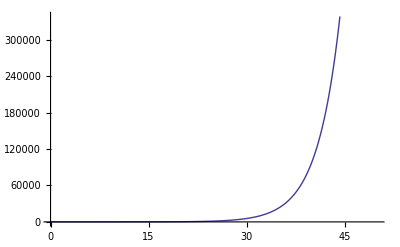

```mathematica
Plot[f[n],{n,0,50}]
```

Clearly the perimeter of the fractal approaches infinitely extremely fast when we iterate.

```mathematica
startlist1 = {{0,0},{3,0}};
startlist2 = {{3,0},{1.5,N[-3 Sqrt[3]/2]}};
startlist3 = {{1.5,N[ -3 Sqrt[3]/2]},{0,0}};
```

```mathematica
koch[{x_,y_}]:={{x,x+(y-x)/3},
{x+(y-x)/3,( y+x)/2 + N[(Sqrt[3]/2)]{(-1/3)(y-x)[[2]],(1/3)(y-x)[[1]]}},{( y+x)/2 +N[(Sqrt[3]/2)]{(-1/3)(y-x)[[2]],(1/3)(y-x)[[1]]},x+(2/3)(y-x)},{x+(2/3)(y-x),y}}
```

```mathematica
iterate[list_]:= Flatten[Map[koch,list],1]
```

```mathematica
newlist[n_]:= Nest[iterate,{startlist1,startlist2,startlist3},n];
```

```mathematica
snowflake[n_]:=Graphics[Line/@newlist[n]]
```

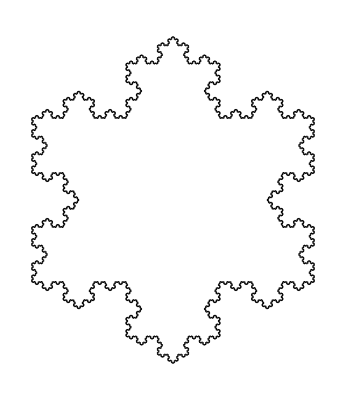

```mathematica
snowflake[5]
```